# Primerjava rodnosti v Sloveniji in na Madžarskem

## Avtorica : Pavlina Šifrar Datum : avgust 2025 Predmet: ROM

## Uvod

## Rodnost in demografske spremembe

Rodnost (nataliteta) je eden od treh ključnih vplivov na rast števila prebivalstva in njegovo starostno sestavo. Poleg rodnosti na naravno rast prebivalstva vplivata še umrljivost in selitve. Razumevanje in spremljanje trendov rodnosti ter dejavnikov, ki jo oblikujejo, je pomembno za načrtovanje družinske politike, pokojninskega sistema, pa tudi gospodarskih in socialnih politik.

Celotna stopnja rodnosti (TFR – Total Fertility Rate) je povprečno število živorojenih otrok na eno žensko v rodni dobi (15-49 let) v koledarskem letu. Celotna rodnost je pomemben in najpogosteje uporabljan kazalnik rodnosti. Npr. vrednost 1,6 pomeni, da bi navidezna generacija 1000 žensk, ki ne bi bila podvržena umrljivosti in selivnosti, rodila 1600 otrok oziroma 1,6 otroka vsaka. Ta kazalnik kaže, ali se bo število prebivalcev dolgoročno povečevalo, ohranjalo ali zmanjševalo. Za preprosto obnavljanje prebivalstva bi morala TFR znašati vsaj 2,1, vendar večina evropskih držav že dalj časa ne dosega te vrednosti. Posledice tega so staranje prebivalstva, manjša delovno aktivna populacija in številni drugi demografski in ekonomski izzivi.


## Namen projektne naloge

Namen raziskave je s pomočjo statističnih podatkov o celotni stopnji rodnosti (TFR) in povprečni starosti žensk ob rojstvu prvega otroka analizirati trende rodnosti v Sloveniji in na Madžarskem ter ugotoviti, kakšen vpliv imajo družinske politike na te trende.

Za primerjavo smo izbrali Madžarsko in Slovenijo zaradi izrazito različnega pristopa k družinski politiki. Od leta 2010 dalje je vlada Viktorja Orbána na Madžarskem uvedla obsežen nabor pronatalitetnih ukrepov, med katerimi so:
•	stanovanjske subvencije (CSOK),
•	subvencije za pričakovane otroke,
•	oprostitev davka na promet nepremičnin za družine,
•	dohodninska oprostitev za matere s štirimi ali veè otroki,
•	davčne olajšave za družine,
•	dodatki za otroke in druge oblike finančne podpore.

V Sloveniji pa je bila družinska politika v zadnjih desetletjih manj izrazito usmerjena v neposredno spodbujanje rodnosti, bolj pa v podporo socialni varnosti in usklajevanju družinskega ter poklicnega življenja.

V raziskavi si zastavljamo naslednja ključna vprašanja:
•	Kakšno je trenutno stanje rodnosti v Sloveniji in na Madžarskem?
•	Kako sta se TFR in povprečna starost žensk ob rojstvu prvega otroka spreminjali od leta 2000 do danes?
•	Kakšen je bil vpliv madžarske družinske politike, ki jo je vlada začela izvajati po letu 2010?
•	Zakaj se število prebivalcev na Madžarskem kljub obsežni podpori družinam še vedno zmanjšuje?
•	Kakšne so dolgoročne demografske napovedi za obe državi - zlasti do leta 2100?
•	Ali so družinske politike izpolnile svoja pričakovanja in če ne, zakaj?

## Uvoz in priprava podatkov

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Povprečna starost matere ob rojstvu prvega otroka

```mathematica
sheet = Import["podatki/demo_find__custom_17641756_spreadsheet.xlsx", {"XLSX", "Data", 3}];
leta = ToExpression[sheet[[8, 2 ;;]]];
vrednostiHU = ToExpression[sheet[[10, 2 ;;]]];
vrednostiSI = ToExpression[sheet[[11, 2 ;;]]];
```

## Skupna stopnja rodnosti (TFR) od 2000 do 2023

```mathematica
podatki3=Import["podatki\\unpopulation_dataportal_20250801182155.csv"];
madzarskaPodatki3=Take[podatki3,{2, 25}];
letaHU3=ToExpression/@madzarskaPodatki3[[All,12]];
HU=ToExpression/@madzarskaPodatki3[[All,27]];
slovenijaPodatki3=Take[podatki3,{26,49}];
letaSI3=ToExpression/@slovenijaPodatki3[[All,12]];
SI=ToExpression/@slovenijaPodatki3[[All,27]];
```

## Skupna stopnja rodnosti (TFR) od 2024 do 2100

```mathematica
podatki=Import["podatki\\unpopulation_dataportal_20250801172150.csv"];
madzarskaPodatki=Take[podatki,{2, 78}];
letaHU=ToExpression/@madzarskaPodatki[[All,12]];
tfrHU=ToExpression/@madzarskaPodatki[[All,27]];
slovenijaPodatki=Take[podatki,{79,155}];
letaSI=ToExpression/@slovenijaPodatki[[All,12]];
tfrSI=ToExpression/@slovenijaPodatki[[All,27]];
```

## Skupno število prebivalcev od 2000 do 2100

```mathematica
podatki2=Import["podatki\\unpopulation_dataportal_20250801175714.csv"];
madzarskaPodatki2=Take[podatki2,{2, 102}];
letaHU2=ToExpression/@madzarskaPodatki2[[All,12]];
prbHU=ToExpression/@madzarskaPodatki2[[All,27]];
slovenijaPodatki2=Take[podatki2,{103,203}];
letaSI2=ToExpression/@slovenijaPodatki2[[All,12]];
prbSI=ToExpression/@slovenijaPodatki2[[All,27]];
```

## Osnovna analiza

## Prikaz tabel

```mathematica
Grid[{{"Leto"}~Join~leta,{"Madžarska"}~Join~vrednostiHU,{"Slovenija"}~Join~vrednostiSI},Frame->All]
```

Leto | 2000 | 2001 | 2002 | 2003 | 2004 | 2005 | 2006 | 2007 | 2008 | 2009 | 2010 | 2011 | 2012 | 2013 | 2014 | 2015 | 2016 | 2017 | 2018 | 2019 | 2020 | 2021 | 2022 | 2023
Madžarska | 25.1 | 25.3 | 25.6 | 25.9 | 26.3 | 26.6 | 26.9 | 27.1 | 27.2 | 27.4 | 27.7 | 27.7 | 27.7 | 27.7 | 27.7 | 27.9 | 27.8 | 28. | 28.2 | 28.3 | 28.4 | 28.6 | 28.7 | 28.8
Slovenija | 26.5 | 26.7 | 27.2 | 27.3 | 27.5 | 27.7 | 27.9 | 28.1 | 28.2 | 28.2 | 28.4 | 28.4 | 28.5 | 28.5 | 28.6 | 28.7 | 28.8 | 28.8 | 28.8 | 28.9 | 29. | 29. | 29. | 29.1

Povprečna starost matere ob rojstvu prvega otroka

```mathematica
Grid[{{"Leto"}~Join~letaHU3,{"Madžarska"}~Join~HU,{"Slovenija"}~Join~SI},Frame->All]
```

Leto | 2000 | 2001 | 2002 | 2003 | 2004 | 2005 | 2006 | 2007 | 2008 | 2009 | 2010 | 2011 | 2012 | 2013 | 2014 | 2015 | 2016 | 2017 | 2018 | 2019 | 2020 | 2021 | 2022 | 2023
Madžarska | 1.31964 | 1.31206 | 1.30259 | 1.27548 | 1.28083 | 1.31227 | 1.34113 | 1.32216 | 1.34616 | 1.32124 | 1.25699 | 1.25023 | 1.33432 | 1.34996 | 1.42449 | 1.44644 | 1.51413 | 1.52411 | 1.52176 | 1.53078 | 1.57555 | 1.6053 | 1.55 | 1.48597
Slovenija | 1.25326 | 1.20841 | 1.21005 | 1.20279 | 1.24807 | 1.26286 | 1.3165 | 1.38562 | 1.52894 | 1.53838 | 1.57945 | 1.57002 | 1.58687 | 1.55275 | 1.58133 | 1.57565 | 1.58695 | 1.62167 | 1.60579 | 1.6113 | 1.59406 | 1.64004 | 1.56833 | 1.57612

TFR od 2000–2023

## Graf skupne stopnje rodnosti

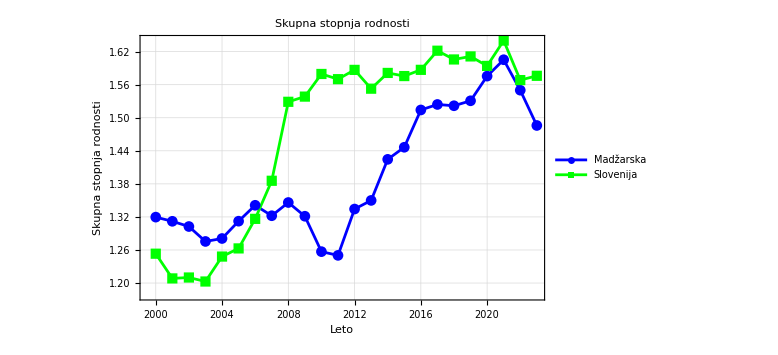

```mathematica
ListLinePlot[{Transpose[{letaHU3,HU}],Transpose[{letaSI3,SI}]},PlotStyle->{Blue, Green},PlotMarkers->Automatic,PlotLegends->Placed[{"Madžarska", "Slovenija"},Above],Frame->True,FrameLabel->{"Leto","Skupna stopnja rodnosti"},PlotLabel->Style["Skupna stopnja rodnosti",Bold,14],GridLines->Automatic,ImageSize->Large]
```

## Graf povprečne starosti ob rojstvu prvega otroka

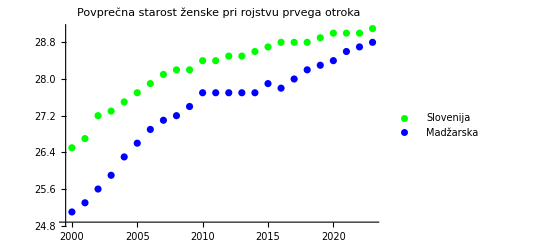

```mathematica
ListPlot[{Transpose[{leta,vrednostiSI}],Transpose[{leta,ToExpression[vrednostiHU]}]},PlotStyle->{Green,Blue},PlotLegends->{"Slovenija","Madžarska"},FrameLabel->{"Leto","TFR"},PlotLabel->"Povprečna starost ženske pri rojstvu prvega otroka"]
```

## Analiza podatkov

```mathematica
(*Funkcija izpiše napovedano TFR za leto 2025 in jo primerja z mejo 2.1.*)preglejLeto2025[leta_,tfr_,prag_:2.1]:=Module[{indeks,vrednost},indeks=FirstPosition[leta,2025][[1]];
vrednost=tfr[[indeks]];
If[vrednost>prag,"Leta 2025 je napovedana TFR "<>ToString[NumberForm[vrednost,{3,2}]]<>", kar presega mejo 2.1 – prebivalstvo bi se lahko obnavljalo.","Leta 2025 je napovedana TFR "<>ToString[NumberForm[vrednost,{3,2}]]<>", kar je pod mejo 2.1 – prebivalstvo se ne bo obnavljalo."]]

(*Primer klica:*)
preglejLeto2025[letaSI,tfrSI]
preglejLeto2025[letaHU,tfrHU]
```

Leta 2025 je napovedana TFR 1.58, kar je pod mejo 2.1 – prebivalstvo se ne bo obnavljalo.

Leta 2025 je napovedana TFR 1.50, kar je pod mejo 2.1 – prebivalstvo se ne bo obnavljalo.

```mathematica
(*Določi posamezna leta,ko povprečna starost žensk narašča ali pada. To pokaže,ali se matere odločajo za otroke kasneje (trend odlašanja materinstva)*)letaPadanjaInRasti[leta_,starosti_]:=Module[{letaRasti={},letaPadanja={}},Do[If[starosti[[i+1]]>starosti[[i]],AppendTo[letaRasti,leta[[i+1]]],If[starosti[[i+1]]<starosti[[i]],AppendTo[letaPadanja,leta[[i+1]]]]],{i,Length[starosti]-1}];
<|"Leta, ko je starost naraščala"->letaRasti,"Leta, ko je starost padala"->letaPadanja|>]

(*Primer klica:*)
letaPadanjaInRasti[leta,vrednostiSI]
letaPadanjaInRasti[leta,vrednostiHU]
```

<|Leta, ko je starost naraščala→{2001,2002,2003,2004,2005,2006,2007,2008,2010,2012,2014,2015,2016,2019,2020,2023},Leta, ko je starost padala→{}|>

<|Leta, ko je starost naraščala→{2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2015,2017,2018,2019,2020,2021,2022,2023},Leta, ko je starost padala→{2016}|>

Naraščanje starosti mater je povezano z odlašanjem materinstva, kar pogosto znižuje končno število otrok

```mathematica
(*Določi posamezna leta,ko TFR narašča ali pada.*)letaPadanjaInRastiTFR[leta_,tfr_]:=Module[{letaRasti={},letaPadanja={}},Do[If[tfr[[i+1]]>tfr[[i]],AppendTo[letaRasti,leta[[i+1]]],If[tfr[[i+1]]<tfr[[i]],AppendTo[letaPadanja,leta[[i+1]]]]],{i,Length[tfr]-1}];
{<|"Gibanje"->"naraščala","Leta"->letaRasti|>,<|"Gibanje"->"padala","Leta"->letaPadanja|>}]

(*Primer klica:*)
letaPadanjaInRastiTFR[letaSI3,SI]
letaPadanjaInRastiTFR[letaHU3,HU]
```

{<|Gibanje→naraščala,Leta→{2002,2004,2005,2006,2007,2008,2009,2010,2012,2014,2016,2017,2019,2021,2023}|>,<|Gibanje→padala,Leta→{2001,2003,2011,2013,2015,2018,2020,2022}|>}

{<|Gibanje→naraščala,Leta→{2004,2005,2006,2008,2012,2013,2014,2015,2016,2017,2019,2020,2021}|>,<|Gibanje→padala,Leta→{2001,2002,2003,2007,2009,2010,2011,2018,2022,2023}|>}

```mathematica
letaPadanjaInRastiTFR[letaSI,tfrSI]
letaPadanjaInRastiTFR[letaHU,tfrHU]
```

{<|Gibanje→naraščala,Leta→{2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2041,2043,2044,2045,2046,2047,2048,2050,2051,2052,2053,2054,2058,2059,2060,2062,2063,2064,2066,2068,2069,2070,2071,2072,2073,2074,2076,2078,2079,2080,2081,2082,2083,2085,2087,2088,2089,2090,2093,2094,2096,2099,2100}|>,<|Gibanje→padala,Leta→{2040,2042,2049,2055,2056,2057,2061,2065,2067,2075,2077,2084,2086,2091,2092,2095,2097,2098}|>}

{<|Gibanje→naraščala,Leta→{2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2057,2058,2059,2060,2061,2062,2064,2065,2066,2067,2068,2069,2071,2072,2074,2075,2076,2080,2083,2084,2085,2088,2090,2095,2096,2097}|>,<|Gibanje→padala,Leta→{2045,2056,2063,2070,2073,2077,2078,2079,2081,2082,2086,2087,2089,2091,2092,2093,2094,2098,2099,2100}|>}

```mathematica
(*Določi posamezna leta,ko prebivalstvo narašča ali pada*)letaPadanjaInRastiPrebivalstva[leta_,prebivalci_]:=Module[{letaRasti={},letaPadanja={}},Do[If[prebivalci[[i+1]]>prebivalci[[i]],AppendTo[letaRasti,leta[[i+1]]],If[prebivalci[[i+1]]<prebivalci[[i]],AppendTo[letaPadanja,leta[[i+1]]]]],{i,Length[prebivalci]-1}];
<|"Leta, ko je prebivalstvo naraščalo"->letaRasti,"Leta, ko je prebivalstvo padalo"->letaPadanja|>]
letaPadanjaInRastiPrebivalstva[letaSI2,prbSI]
letaPadanjaInRastiPrebivalstva[letaHU2,prbHU]
```

<|Leta, ko je prebivalstvo naraščalo→{2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2023,2024},Leta, ko je prebivalstvo padalo→{2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2045,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2081,2082,2083,2084,2085,2086,2087,2088,2089,2090,2091,2092,2093,2094,2095,2096,2097,2098,2099,2100}|>

<|Leta, ko je prebivalstvo naraščalo→{2023},Leta, ko je prebivalstvo padalo→{2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015,2016,2017,2018,2019,2020,2021,2022,2024,2025,2026,2027,2028,2029,2030,2031,2032,2033,2034,2035,2036,2037,2038,2039,2040,2041,2042,2043,2044,2045,2046,2047,2048,2049,2050,2051,2052,2053,2054,2055,2056,2057,2058,2059,2060,2061,2062,2063,2064,2065,2066,2067,2068,2069,2070,2071,2072,2073,2074,2075,2076,2077,2078,2079,2080,2081,2082,2083,2084,2085,2086,2087,2088,2089,2090,2091,2092,2093,2094,2095,2096,2097,2098,2099,2100}|>

## Izris napovedi do 2100

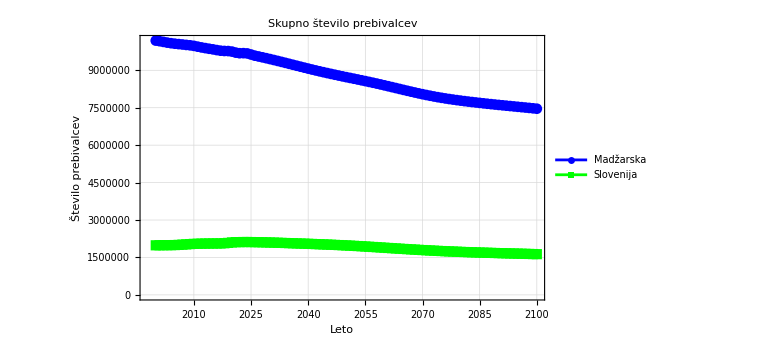

```mathematica
ListLinePlot[{Transpose[{letaHU2,prbHU}],Transpose[{letaSI2,prbSI}]},PlotStyle->{Blue, Green},PlotMarkers->Automatic,PlotLegends->Placed[{"Madžarska", "Slovenija"},Above],Frame->True,FrameLabel->{"Leto","Število prebivalcev"},PlotLabel->Style["Skupno število prebivalcev",Bold,14],GridLines->Automatic,ImageSize->Large]
```

Napoved števila prebivalcev do 2100

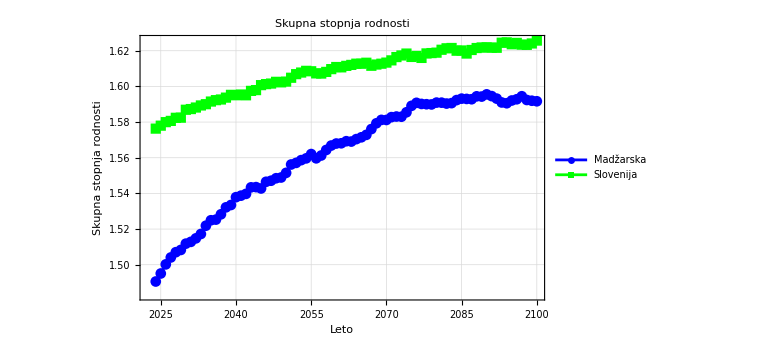

```mathematica
ListLinePlot[{Transpose[{letaHU,tfrHU}],Transpose[{letaSI,tfrSI}]},PlotStyle->{Blue, Green},PlotMarkers->Automatic,PlotLegends->Placed[{"Madžarska", "Slovenija"},Above],Frame->True,FrameLabel->{"Leto","Skupna stopnja rodnosti"},PlotLabel->Style["Skupna stopnja rodnosti",Bold,14],GridLines->Automatic,ImageSize->Large]
```

Napoved TFR do 2100

## Zaključek

## Kaj smo ugotovili • Kakšno je trenutno stanje rodnosti v Sloveniji in na Madžarskem?

V Sloveniji in na Madžarskem se prebivalstvo ne obnavlja saj skupna stopnja rodnosti ne presega meje 2.1. Napovedi za leto 2025 kažejo, da bo TFR za leto 2025 višji v Sloveniji in znašal 1.58, na Madžarskem pa 1.50.  Napovedi kažejo, da se bo TRF do leta 2100 v obeh državah zviševala vendar ne bo dosegla meje 2.1. (ta meja predstavlja število otrok, ki jih ženska rodi v rodni dobi (15-49 let), 0.1 je dodano zaradi umrljivosti). Torej kljub temu, da se TFR viša, ker je njegova vrednost manjša od 2.1 bo prebivalstvo upadalo.

## • Kako sta se TFR in povprečna starost žensk ob rojstvu prvega otroka spreminjali od leta 2000 do 2023?

TFR je v Sloveniji naraščala leta: 2002, 2004, 2005, 2006, 2007, 2008, 2009, 2010, 2012, 2014, 2016, 2017, 2019, 2021, 2023, padala leta: 2001, 2003, 2011, 2013, 2015, 2018, 2020, 2022.
TFR je na Madžarskem naraščala leta: 2004, 2005, 2006, 2008, 2012, 2013, 2014, 2015, 2016, 2017, 2019, 2020, 2021, padala leta: 2001, 2002, 2003, 2007, 2009, 2010, 2011, 2018, 2022, 2023.
Povprečna starost žensk ob rojstvu prvega otroka je v Sloveniji vsa leta naraščala, na Madžarskem pa je padala le leta 2016.

## • Kakšen je bil vpliv madžarske družinske politike, ki jo je vlada začela izvajati po letu 2010?

S podatkov o TFR lahko razberemo, da je družinska politika na Madžarskem pozitivno vplivala na rodnost saj se je TFR iz leta 2011 do leta 2021 dvignil z 1.25 na 1.605, vendar je začel po letu 2021 strmo upadati in je leta 2023 dosegel vrednost 1.486. Predikcije kažejo, da se bo TFR do leta 2100 sicer stalno zviševalo vendar bo leta 2100 doseglo vrednost 1.592, kar ne dosega potrebne meje 2.1

## • Zakaj se število prebivalcev na Madžarskem kljub obsežni podpori družinam še vedno zmanjšuje?

Po opravljeni raziskavi smo opazili, da je družinska politika na Madžarskem pozitivno vplivala na zviševanje stopnje rodnosti, vendar ne dovolj saj brez drugih ukrepov še dolgo ne bo dosegla meje 2.1. Eden od razlogov za nezadosten uspeh družinske politike bi lahko bil, da finančna situacija parov ne vpliva v takšni meri na pare, da bi se odločili za večje število otrok. Morda v večji meri vplivajo osebne vrednote in verska pripadnost. Velika večina mladih ima za prioriteto kariero in ne ustvarjanja velike družine, zato jih finančna podpora ne spodbudi dovolj.

## • Kakšne so dolgoročne demografske napovedi za obe državi - zlasti do leta 2100?

V Sloveniji pozitivna neto migracija nekoliko ublaži naravni upad prebivalstva, na Madžarskem pa negativne migracije pospešujejo zmanjševanje prebivalstva. Zato bo do leta 2100 upad na Madžarskem izrazitejši.

## Možnosti za nadaljnjo analizo

Nadalje bi lahko analizirali vpliv religije na število rojstev matere ali poskusili raziskati glavne vrednote in cilje in ugotoviti ali imajo res tako velik vpliv na odločitev o otrocih in zakaj je temu tako.

## Viri

Eurostat:https://ec.europa.eu/eurostat
UN WPP:https://population.un.org/wpp/